```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
```

# Fig 2

```mathematica
file=path<>"circles_data.hdf5";
data=Import[file, "Data"];
power = data["/power"];
freq = data["/freq"];
refl=data["/R_real"]+I data["/R_imag"];
```

```mathematica
powerRef=0;
npower=Length[power];
nfreq=Length[freq];
MinFreq=Min[freq];
MaxFreq=Max[freq];
MinPowerInd=1;
MaxPowerInd=npower;
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,MinPowerInd,MaxPowerInd},{l,0,1},{j,1,nfreq}];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{f0→6.54453,Γ→0.00174249,p→0.782264,α→5.56783×10^-7}

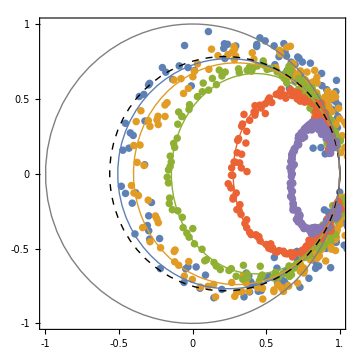

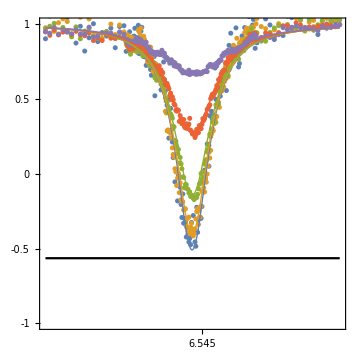

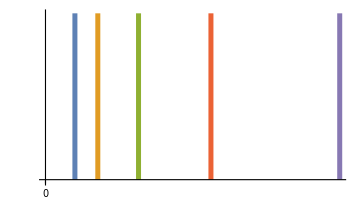

```mathematica
fit=FindFit[Flatten[tofit,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,0.00186},{p,0.793},{α,0.003}},{f,P,s}]
PlotIndices={1,2,3,4,5};
ΩRabi =10^3 √(α 10^((power[[MinPowerInd;;MaxPowerInd]]-powerRef)/10))/.fit;

g1=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-1]],tofit[[i,2,;;,-1]]},{i,PlotIndices}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->PointSize[0.015]],
ParametricPlot[Evaluate@Table[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]}/.fit,{i,PlotIndices}],{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Thick],
ParametricPlot[Evaluate@{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Black,Thick,Dashed]],
ParametricPlot[Evaluate@{Re[1-(2 Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2  Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Gray,Thick]]
,Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1.0},None}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

g2=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-4]],tofit[[i,1,;;,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{MinFreq,MaxFreq},{-1,1}}],Plot[Evaluate@Table[Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,MinFreq,MaxFreq},PlotRange->All,PlotStyle->Thick],
Plot[1-2p/.fit,{f,MinFreq,MaxFreq},PlotStyle->Black],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[6.53+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->1,ImageSize->Medium]


g3=ParametricPlot[Evaluate[{#,x}&/@ΩRabi],{x,-0,0.5},PlotStyle->Thickness[0.01],Ticks->{Table[i,{i,0,10}],None},TicksStyle->Directive[Black,"Arial", 14]]
```

```mathematica
Export[path<>"circles.eps",g1]
Export[path<>"circles_real_part.eps",g2]
Export[path<>"Omega_rabi.eps",g3]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles_real_part.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\Omega_rabi.eps

# Fig 3

```mathematica
FixedUpperBound=Mean[{0.7133940085771162,0.4866773887549828+0.275317557041368}];
FixedLowerBound=Mean[{0.7133940085771162-0.4876694481415331,0.4866773887549828-0.275317557041368}];
```

```mathematica
PtSize=0.035;
```

## Rabi

```mathematica
file=path<>"rabi_data.hdf5";
data=Import[file, "Data"];
delays = data["/x"];
population = data["/y"];
```

{A→0.259576,B→0.478118,Ω→0.00598864,ϕo→-0.0834947,TR→415763.}

83.4914

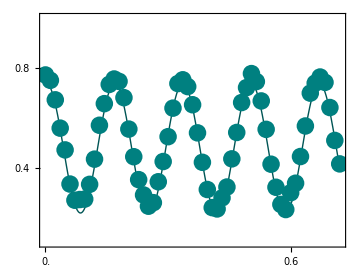

```mathematica
fit=FindFit[Transpose[{delays,population}],{A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{A==(FixedUpperBound-FixedLowerBound)/2,B==(FixedUpperBound+FixedLowerBound)/2}},{{A,0.3},B,{Ω,0.004},{ϕo,0},{TR,1000}},t]
Pratio01=(B2-A2)/(B2+A2);
P0ini=0.5;
r0=0.5;
1/(Ω)/2/.fit
g=Show[Plot[(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B)*(P0ini/r0)/.fit,{t,0,delays[[-1]]/1000}, PlotStyle->Directive[Darker@RGBColor[0,0.5,0.5],Thick],PlotRange->{0.1,1}],ListPlot[Transpose@{delays/1000,population*(P0ini/r0)}, PlotStyle->{PointSize[PtSize],RGBColor[0,0.5,0.5]}],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"rabi.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\rabi.eps

## T1

```mathematica
file=path<>"t1_ramsey_echo_data.hdf5";
data=Import[file, "Data"];
delays = data["/x"];
population = data["/y"];
T1Population=population[[1]];
T2RamseyPopulation=population[[2]];
T2Population=population[[3]];
```

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | -0.519152 | 0.0116581 | {-0.542996,-0.495309}
B | 0.737694 | 0.00735354 | {0.722655,0.752734}
TR | 51719. | 2634.53 | {46330.8,57107.2}

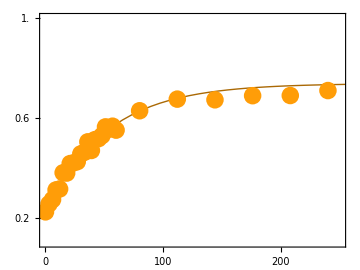

```mathematica
scale=P0ini/r0;
initguessS={{A,0.5},{B,0.8},{TR,50000}};
BoundS={A==FixedLowerBound-FixedUpperBound,B==FixedUpperBound,TR>0};
model=A*Exp[-t/TR]+B;
data=Transpose[{delays,T1Population*scale}];
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays/1000,T1Population*scale}];
g=Show[Plot[((nmf[t*1000]/.sparam)),{t,0,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#FF9D08"],Thick],PlotRange->{{0,250},{0.1,1}}],ListPlot[dataS,PlotStyle->Directive[PointSize[PtSize],RGBColor["#FF9D08"]]],FrameTicks->{{Table[0.2i,{i,-5,5}],None},{Table[50i,{i,0,7}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"t1.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\t1.eps

## T2

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | 0.259576 | 0.00922524 | {0.240708,0.278444}
B | 0.478118 | 0.00582737 | {0.4662,0.490037}
TR | 51859.9 | 4185.76 | {43299.,60420.7}

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | -0.259576 | 0.0137878 | {-0.287866,-0.231286}
B | 0.478118 | 0.00316669 | {0.471621,0.484616}
TR | 26303.5 | 2357.35 | {21466.7,31140.4}
Ω | 0.0000297344 | 6.42547×10^-7 | {0.000028416,0.0000310527}
ϕo | 0.0709616 | 0.0740053 | {-0.0808848,0.222808}

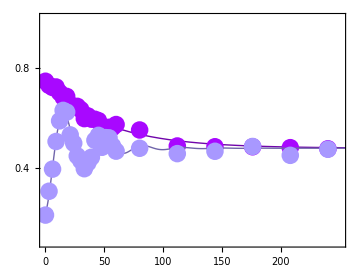

```mathematica
data=Transpose[{delays,T2Population*scale}];
BoundS={A==(-FixedLowerBound+FixedUpperBound)/2,B==(FixedUpperBound+FixedLowerBound)/2,TR>0};
initguessS={{A,0.5},{B,0.8},{TR,50000}};
model=A*Exp[-t/TR]+B;
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays/1000,T2Population*scale}];
dataRamsey=Transpose[{delays,T2RamseyPopulation*scale}];
BoundS={A==-(-FixedLowerBound+FixedUpperBound)/2,B==(FixedUpperBound+FixedLowerBound)/2,TR>0,0.001>Ω>0};
modelRamsey=A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B;
initguessS={{A,0.5},{B,0.8},{TR,50000},{Ω,0.00002973452815432999},{ϕo,0}};
nmfRamsey=NonlinearModelFit[dataRamsey,{modelRamsey,BoundS},initguessS,t];
sparamRamsey=nmfRamsey["BestFitParameters"];
nmfRamsey["ParameterConfidenceIntervalTable"]
dataSRamsey=Transpose[{delays/1000,T2RamseyPopulation*scale}];
g=Show[Plot[(nmf[t*1000]/.sparam),{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#A808FF"],Thick],PlotRange->{{0,250},{0.1,1}}],ListPlot[dataS,PlotStyle->Directive[RGBColor["#A808FF"],PointSize[PtSize]]], Plot[(nmfRamsey[t*1000]/.sparamRamsey),{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#A898FF"],Thick],PlotRange->{{0,250},{0.1,1}}],ListPlot[dataSRamsey,PlotStyle->Directive[RGBColor["#A898FF"],PointSize[PtSize]]],Frame->True,FrameTicks->{{Table[0.2i,{i,0,8}],None},{Table[50i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"t2.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\t2.eps

# Fig 4

```mathematica
file=path<>"transient_data0.hdf5";
data=Import[file, "Data"];
(*delays = Join[data["/time0"],data["/time"]];*)
delays = data["/time"];
power=data["/power"]
population=data["/y"];
(*population= Join[data["/y0"],data["/y"]]*)
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={1>A>-1,1>B>0,TR>0};
model=A*Exp[-t/TR]+B;
numberloop=6;
delays=delays[[;;numberloop]];
power=power[[;;numberloop]];
population=population[[;;numberloop]];
numberloop=Length[population];
fit=Table[NonlinearModelFit[Transpose[{delays[[loopi,3;;]],population[[loopi,3;;]]}],{model,BoundS},initguessS,t],{loopi,1,numberloop}];
Tpump=Table[TR/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}]
σTpump=Table[fit[[loopi]]["ParameterErrors"][[3]],{loopi,1,numberloop}]
Gpump=1/(2*Pi*Tpump);
Amp=Table[A/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}]
Bs=Table[B/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}];
```

{-40.,-35.,-30.,-25.,-20.,-15.,-10.}

{38621.5,26865.2,14765.5,7499.04,6364.46,5747.12}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{3439.74,1241.32,573.916,286.474,280.343,286.009}

{0.145485,0.299915,0.461674,0.545811,0.546073,0.501339}

```mathematica
0.3551*^-3/2/π
```

0.0000565159

{G10→2.02549×10^-6,G21→0.0000547029,a→0.000998457}

| Estimate | Standard Error | Confidence Interval
G10 | 2.02549×10^-6 | 1.30537×10^-6 | {-2.12878×10^-6,6.17976×10^-6}
G21 | 0.0000547029 | 2.98539×10^-6 | {0.000045202,0.0000642037}
a | 0.000998457 | 0.000249325 | {0.000204995,0.00179192}

78576.2

2909.44

5.81889

branching ratio 33.0353

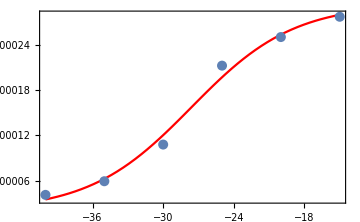

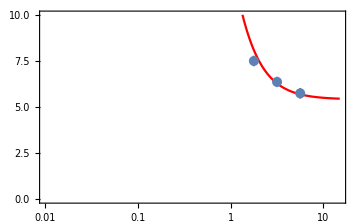

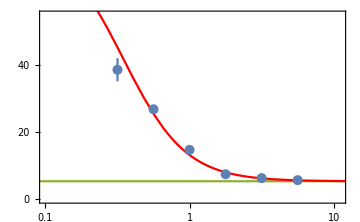

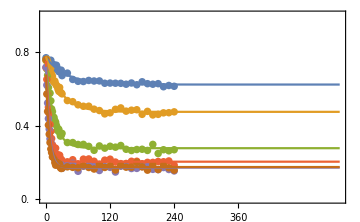

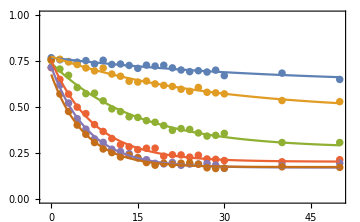

```mathematica
T1guess=150634.93060222779;
G20=0.0018071254414408456;
G10guess=1/(2*Pi*T1guess);
initguessS={{G10,G10guess},{G21,0.3551*^-3/2/π},{a,9.827*^-3/(2π)^2}};
BoundS={1/(2*Pi*1*10^4)>G10>1/(2*Pi*10*10^4),0.00008>G21>0.00002,0.0005>a>0.0001};
model=G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10))));
(*Gfit2=FindFit[Transpose[{power,Gpump}],{G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10))))
,BoundS},{{G10, G10guess},{G21,0.0005}, {a,0.002}},p,AccuracyGoal->50]*)
nmf=NonlinearModelFit[Transpose[{power,Gpump}],{model},initguessS,p];
(*Gfit2={G10->initguessS[[1,2]],G21->initguessS[[2,2]],a->initguessS[[3,2]]}*)
Gfit2=nmf["BestFitParameters"]
nmf["ParameterConfidenceIntervalTable"]
G10fix=G10/.Gfit2;
T1fix=1/(2π G10fix)
1/(2π G21)/.Gfit2
10^-3/(π G21)/.Gfit2
"branching ratio "<>ToString[G20/G21/.Gfit2]
Show[Plot[(G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10)))))/.Gfit2,{p,Min[power],Max[power]}, PlotRange->All,PlotStyle->Red],
ListPlot[Transpose[{power,Gpump}],PlotStyle->PointSize[0.02]]
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]

Omega=Sqrt[a*10^(power/10)]/.Gfit2;
toplotT=Table[{{10^3 Omega[[i]],10^-3 Tpump[[i]]},ErrorBar[10^-3 σTpump[[i]]]},{i,1,Length@power}];

branching=Show[LogLinearPlot[10^-3/(2*Pi*(G10+(G21*(Ω*10^-3)^2/((G20+G21)^2+2*(Ω*10^-3)^2))))/.Gfit2,{Ω,0.01,15}, PlotRange->{0,10},PlotStyle->Red],
ErrorListLogLinearPlot[toplotT,PlotStyle->PointSize[0.02]]
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]

branching=Show[LogLinearPlot[{10^-3 T1fix,10^-3 T1fix,10^-3/(π G21+2π G10fix)/.Gfit2},{x,0.01,15}, FrameTicks->{{Table[0+10i,{i,0,5}],None},{{0.1, 0.32,1,3.2,10},None}},PlotStyle->{None,Automatic,Automatic}],LogLinearPlot[10^-3/(2*Pi*(G10+(G21*(Ω*10^-3)^2/((G20+G21)^2+2*(Ω*10^-3)^2))))/.Gfit2,{Ω,0.01,15}, PlotRange->All,PlotStyle->Red],
ErrorListLogLinearPlot[toplotT,PlotStyle->PointSize[0.02]],PlotRange->{{Log[0.1],Log[11]},{0,55}}
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]
g=Show[ListPlot[Table[Transpose[{10^-3 delays[[loopi]],population[[loopi]]}],{loopi,1,numberloop}],PlotRange->{{-1,550},{0,1}},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,0,550}],Frame->True,FrameTicks->{{Table[0.2i,{i,0,5}],None},{Table[40i,{i,0,10}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

Show[ListPlot[Table[Transpose[{10^-3 delays[[loopi]],population[[loopi]]}],{loopi,1,numberloop}],PlotRange->{{-1,50},{0,1}},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,0,50}],Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

```mathematica
Export[path<>"branching0.eps",branching]
Export[path<>"branching0.png",branching]
Export[path<>"transient0.eps",g]
Export[path<>"transient0.png",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\branching0.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\branching0.png

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\transient0.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\transient0.png

```mathematica
Manipulate[Show[ListPlot[Transpose[{power,Gpump}],PlotStyle->PointSize[0.02]],Plot[G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10)))),{p,-40,-10}, PlotRange->Automatic,PlotStyle->Red]
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]],{G10,1*^-7,1*^-5},{G21,1*^-6,1*^-4},{G20,0.0001,0.01},{a,0.00001,.01}]
```

```mathematica
Simplify[(10^3 2*Pi)^2*a*10^3/.Gfit2]/.p->-60
```

9.827×10^7